# Reorganization energy for a redox molecule near metal electrode

## Point charge at the center of a cylindrical cavity

## Units

```mathematica
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

## Parameters

Dielectric permittivities:
solvent statis: ϵ_s
solvent optical: ϵ_∞
SAM: ϵ_m
metal electrode: ∞

```mathematica
ϵs=78;
ϵinf=1.78;
ϵm=2.25;
```

## Cylindrical model without SAM

```mathematica
Clear[λ,λd]
```

λ [dq, a, b, d] - Reorganization energy for a point charge (kcal/mol):
a,b - parameters of the cylindrical cavity around the redox molecule (Å);
d - distance from the center of the cavity to the electrode surface (Å);
dq - absolute change in total charge in a.u. (number of electrons transferred);

```mathematica
λ[dq_,a_,b_,d_]:=Module[{F0,R,A,B,x,γ},
R=d a2bohr;
A=a a2bohr;
B=b a2bohr;
F0=1/ϵinf-1/ϵs;
x=(2R-B-√(A^2+(2R-B)^2))/(2R+B-√(A^2+(2R+B)^2));
γ=1/(A(2B+A))(4R-2B+2 √(A^2+B^2)-√(A^2+(2R-B)^2)-√(A^2+(2R+B)^2)+2ArcSinh[B/A]-Log[x]);
1/2 dq^2 F0 γ au2kcal
];
```

```mathematica
λ[1,3,2,5]
```

11.9553

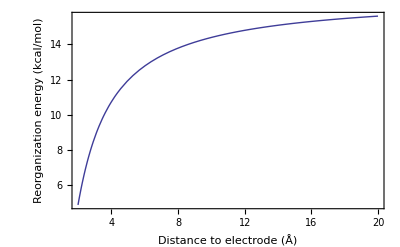

```mathematica
Plot[λ[1,3,2,d],{d,2,20},Axes->False,Frame->True,FrameLabel->{"Distance to electrode (Å)","Reorganization energy (kcal/mol)"}]
```

λd [dq, a, b, d] - Reorganization energy for a point dipole (kcal/mol):
r - dipole length (Å);
a,b - parameters of the cylindrical cavity around the redox molecule (Å);
d - distance from the center of the cavity to the electrode surface (Å);
dq - absolute change in total charge in a.u. (number of electrons transferred);

```mathematica
λd[dq_,r_,a_,b_,d_]:=Module[{F0,R,A,B,x,γ},
R=d a2bohr;
A=a a2bohr;
B=b a2bohr;
F0=1/ϵinf-1/ϵs;
x=4 r+2 √(4 A^2+(-2 B+r)^2)-2 √(4 A^2+(2 B+r)^2)-√(4 A^2+(-2 B-4 R+r)^2)+√(4 A^2+(2 B-4 R+r)^2)-√(4 A^2+(-2 B+4 R+r)^2)+√(4 A^2+(2 B+4 R+r)^2)+2 Log[(2 B-r+√(4 A^2+(-2 B+r)^2))/(-2 B-r+√(4 A^2+(2 B+r)^2))]-2 (Log[(2 B+r+√(4 A^2+(2 B+r)^2))/(-2 B+r+√(4 A^2+(-2 B+r)^2))]+Log[-2 B-4 R+r+√(4 A^2+(-2 B-4 R+r)^2)]-Log[2 B-4 R+r+√(4 A^2+(2 B-4 R+r)^2)]+Log[(2 B+4 R+r+√(4 A^2+(2 B+4 R+r)^2))/(-2 B+4 R+r+√(4 A^2+(-2 B+4 R+r)^2))]);
γ=x/(2A(2B+A));
1/2 dq^2 F0 γ au2kcal
];
```

```mathematica
λd[2,0.5,3,2,5]
```

4.33684

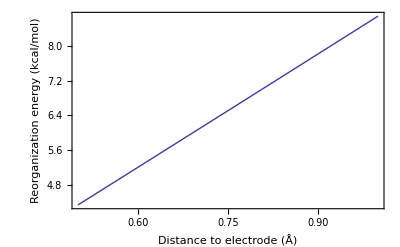

```mathematica
Plot[λd[2,r,3,2,5],{r,0.5,1.0},Axes->False,Frame->True,FrameLabel->{"Distance to electrode (Å)","Reorganization energy (kcal/mol)"}]
```

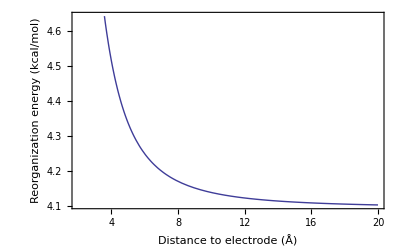

```mathematica
Plot[λd[2,0.5,3,2,d],{d,2,20},Axes->False,Frame->True,FrameLabel->{"Distance to electrode (Å)","Reorganization energy (kcal/mol)"}]
```